# Additional 2D Constructions

## Comprehension Questions

Math 250 - Math with Mathematica
Christopher Hanusa

### 9-1. Draw the curve y=x^3+2 x^2+x+1 and place a point on it.

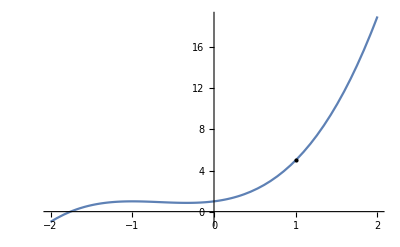

Important reminder: When you need to combine multiple Graphics objects, use the Show command.

### 9-2. Use a BSplineCurve command to make a circle-like curve.

```mathematica
points={{0,0},{1,0},{1,1},{0,1}};
Graphics[{{Red, PointSize[.05],Map[Point,points]},{Green, Line[points]},BSplineCurve[points,SplineClosed->True]}]
```

-Graphics-

```mathematica
points={{0,0},{0.9,0},{1,0},{1,1},{0,1}};
Graphics[{{Red, PointSize[.05],Map[Point,points]},{Green, Line[points]},BSplineCurve[points,SplineClosed->True]}]
```

-Graphics-

```mathematica
epsilon=0.1;
points={{0,0},{epsilon,0},{1-epsilon,0},{1,0},{1,epsilon},{1,1-epsilon},{1,1},{1-epsilon,1},{epsilon,1},{0,1},{0,1-epsilon},{0,epsilon}};
Graphics[{{Red, PointSize[.05],Map[Point,points]},{Green, Line[points]},BSplineCurve[points,SplineClosed->True]}]
```

-Graphics-

```mathematica
epsilon=0.2;
points={{epsilon,0},{1-epsilon,0},{1,epsilon},{1,1-epsilon},{1-epsilon,1},{epsilon,1},{0,1-epsilon},{0,epsilon}};
Graphics[{(*Red, PointSize[.05],Map[Point,points]},{Green, Line[points]},*)BSplineCurve[points,SplineClosed->True]}]
```

-Graphics-

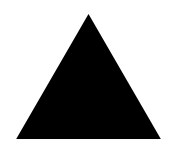

```mathematica
Graphics[RegularPolygon[3]]
```

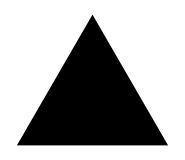

```mathematica
vertices={{-1,0},{1,0},{0,Sqrt[3]}};
Graphics[Polygon[vertices]]
```

### Here are the coordinates of the vertices (p1,p2,p3) and the vectors from p1 to p2, etc.

```mathematica
p1=vertices[[1]];
p2=vertices[[2]];
p3=vertices[[3]];
```

```mathematica
v12=vertices[[2]]-vertices[[1]];
v12=v12/Norm[v12]
```

{1,0}

```mathematica
v23=vertices[[3]]-vertices[[2]];
v23=v23/Norm[v23]
```

{-1/2,(√3)/2}

```mathematica
v31=vertices[[1]]-vertices[[3]];
v31=v31/Norm[v31]
```

{-1/2,-(√3)/2}

```mathematica
epsilon=0.5;
points={p1,p1+epsilon*v12,p2-epsilon*v12,p2,p2+epsilon*v23,p3-epsilon*v23,p3,p3+epsilon*v31,p1-epsilon*v31};
Graphics[{{Red, PointSize[.05],Map[Point,points]},{Green, Line[points]},BSplineCurve[points,SplineClosed->True]}]
```

-Graphics-

```mathematica
epsilon=0.2;
points={p1+epsilon*v12,p2-epsilon*v12,p2+epsilon*v23,p3-epsilon*v23,p3+epsilon*v31,p1-epsilon*v31};
Graphics[{(*{Red, PointSize[.05],Map[Point,points]},{Green, Line[points]},*)BSplineCurve[points,SplineClosed->True]}]
```

-Graphics-

### 9-3. Create a two-dimensional region that has the curve from Question 9-2 as its boundary.

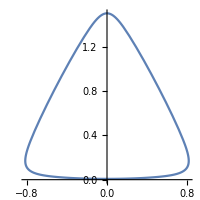

```mathematica
curve=ParametricPlot[BSplineFunction[points,SplineClosed->True][t],{t,0,1},ImageSize->200]
```

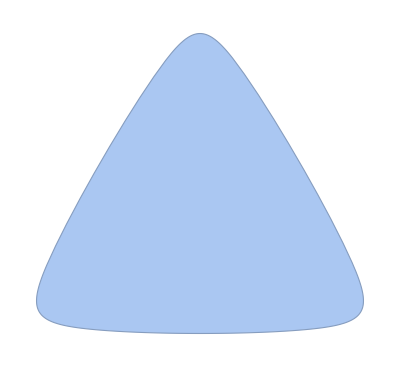

```mathematica
shape=BoundaryDiscretizeGraphics[curve]
```

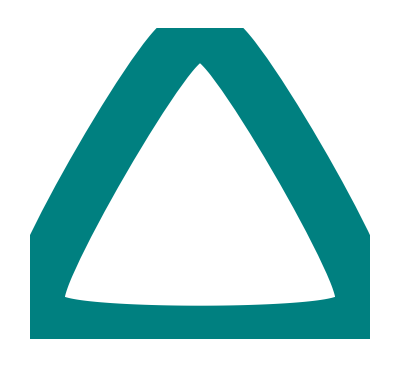

```mathematica
Graphics[{EdgeForm[{Thickness[.1],Blend[{Blue,Green}]}],White,shape}]
```

### 9-4. Plot the two curves y=√x and y=x^2 for x between 0 and 1 on the same set of axes.

### 9-5. Use RegionPlot to draw the region that is between the two curves from Question 9-4.